基礎庫 :

```mathematica
<<(FileNameJoin[{$UserDocumentsDirectory,"Wolfram Mathematica","ssrlib.wl"}])
```

## 留存

```mathematica
ClearAll[keepMarkData];
keepMarkData = Base`excleData[modelPath,"keep","mark"][Select[#day!=""&],All];
lvKeep = Base`excleInterpolation[keepMarkData,"day"->lvToday[#],"非"]&;
```

```mathematica
Export[FileNameJoin[{basePath,"keep.txt"}],lvKeep/@Range[30],"Table"]
```

C:\ssr-config\trunk\config\designer\keep.txt

Open[C:\ssr-config\trunk\config\designer\keep.txt]

## 付费模型

```mathematica
ClearAll[];
```

```mathematica
ltv[0.28,1]
```

0.28

## 付费期望

```mathematica
ClearAll[paymentconfig,buisnessData,portraitconfig,userPay,userProp,userNum,userKeep,income,recycle,payExpect,ltv,payment];
paymentconfig = Base`excleData[modelFile,"pay","payment"][Select[#id!=""&],All];
buisnessData = Base`excleData[modelFile,"benchmark","base"][Select[#day!=""&],All];
portraitconfig = Base`excleData[modelFile,"pay","portrait"][Select[#id!=""&],All];
userPay = Normal@portraitconfig[All,"dayArpu"];
userProp = Normal@portraitconfig[All,"proportion"];
userNum[day_]:= Module[{num=Normal@portraitconfig[All,Min[#userNum,#userNum*If[day<=1,1,day^(#keep-1)/(1/#keep)^0.5]]&],keep=paymentconfig[First,"单服人数"]*Base`excleInterpolation[buisnessData,"day"->day,"keep"],deviate,space},deviate=keep-Total@num;space=Normal@portraitconfig[All,"userNum"]-num;
                        deviate *=Normalize[If[deviate>0,space,num],Total];
                        Max[#,0]&/@(num+deviate)];
userKeep = Table[N[Total@userNum[n]/Total@userNum[1]],{n,{2,3,7,14,30,60,180,360}}];
income[day_/;day>=1] := ltv[day]*Total[userNum[1]];
income[day_/;day<1]:= 0;

payExpect[day_]:= (income[day]-income[day-1])*Normalize[userPay*Normal@portraitconfig[All,"keep"]*userNum[day],Total]/userNum[day];
recycle = Module[{n=1,cost=paymentconfig[First,#"预估成本"*#"单服人数"*#"成本风险"&]*1.5},While[income[n]<cost,n++];n];
{"recycle"->recycle,"roi"-> (Total@Sum[Total[Flatten[payExpect[n]*userNum[n]]],{n,1,recycle}]/paymentconfig[First,#"预估成本"*#"单服人数"*#"成本风险"&])}
payment[day_]:=Base`joinDataset[{portraitconfig[All,{"name","userNum","dayArpu"}],Base`createDataset[{"活跃人数","人数占比%","付费占比","最高付费"},{userNum[day],100*Normalize[Flatten@userNum[day],Total],Normalize[Flatten@Sum[userNum[n]*payExpect[n],{n,1,day}],Total],Flatten@Sum[payExpect[n],{n,1,day}]}]}];
```

{recycle→1,roi→Total[Total[(ltv[1] (Max[0,(If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12228,num$12228] (-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]))/Total[If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12228,num$12228]]]+Max[0,Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]) (Max[0,(If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12230,num$12230] (-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]))/Total[If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12230,num$12230]]]+Max[0,Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]) Total[Max[0,(If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12227,num$12227] (-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]))/Total[If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12227,num$12227]]]+Max[0,Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]] Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,dayArpu] Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,keep])/((Max[0,(If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12229,num$12229] (-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]))/Total[If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12229,num$12229]]]+Max[0,Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]) Total[(Max[0,(If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12228,num$12228] (-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]))/Total[If[-Total[Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]+Base`excleInterpolation[Base`excleData[modelFile,benchmark,base][Select[#day≠&],All],day→1,keep] Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,单服人数]>0,space$12228,num$12228]]]+Max[0,Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,Min[#userNum,#userNum If[1≤1,1,1^(#keep-1)/(1/(#keep))^0.5]]&]]) Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,dayArpu] Base`excleData[modelFile,pay,portrait][Select[#id≠&],All][All,keep]])]]/Base`excleData[modelFile,pay,payment][Select[#id≠&],All][First,#预估成本 #单服人数 #成本风险&]}

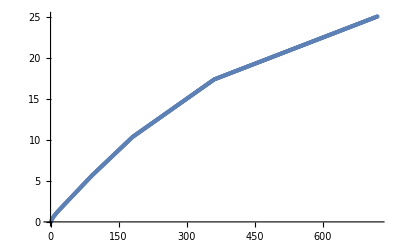

```mathematica
ListPlot@Table[ltv[n],{n,0,720}]
```

```mathematica
payment[1]
```

## 运营演算

```mathematica
ClearAll[operatData,ssData,dau,totalIncome,arpu];
ssData = Base`excleData[modelFile,"benchmark","ss"];
operatData = Base`excleData[modelFile,"pay","operation"];
dau[day_Integer,import_Integer]:= import/paymentconfig[First,"单服人数"]*Total[userNum[#]&/@Array[#&,day]];
dau[day_Integer]:= Total[userNum[#]&/@Array[#&,day]];
dau[import_List]:= Sum[import[[n]]/paymentconfig[First,"单服人数"]*userNum[n],{n,1,Length[import]}];
totalIncome[day_Integer,import_Integer]:= import/paymentconfig[First,"单服人数"]*Total[income[#]&/@Array[#&,day]];
totalIncome[day_Integer]:= Total[income[#]&/@Array[#&,day]];
totalIncome[import_List]:= Sum[import[[n]]/paymentconfig[First,"单服人数"]*income[n],{n,1,Length[import]}];
monthIncome[import_List]:= totalIncome[Flatten[Table[#,30]&/@import]];
arpu[day_]:= (income[day]-income[day-1])/Total[userNum[day][[;;-2]]];
```

```mathematica
Table[(monthIncome[Normal[operatData[1;;n,"import"]]]-monthIncome[Normal[operatData[1;;n-1,"import"]]]),{n,1,12}]
```

{4.39656×10^6,1.0172×10^7,1.94262×10^7,3.39835×10^7,4.43992×10^7,5.31154×10^7,5.51541×10^7,5.98136×10^7,6.42643×10^7,6.28042×10^7,6.51619×10^7,6.33523×10^7}

## 用户画像

```mathematica
ClearAll[portraitName,userPortrait,userPortNum,userPortPay];
portraitName = {"A类","B类","C类","D类","非核心"};
userPortrait = Base`excleData[modelFile,"pay","portrait"][GroupBy["id"],First,portraitName][All,Normalize[#,Total]&];
userPortNum[day_Integer]:= Transpose[userPortrait][All,Times[#,AssociationThread[userLayerID,userNum[day]]]&]//Transpose;
userPortPay[day_Integer]:= Transpose[userPortrait][All,Times[#,Normal[Base`mergeDataset[{userPerDay[Range[day]],payPerDay[Range[day]]},Times][Total,All]]]&]//Transpose;
```

```mathematica
userPortPay[recycle][Total,All]
```

540213.

## Data导出

```mathematica
Export[FileNameJoin[{basePath,"_data","payPerDay.txt"}],Prepend[Table[payExpect[n],{n,1,maxDay}],Normal@portraitconfig[All,"id"]],"Table"];
Export[FileNameJoin[{basePath,"_data","userPerDay.txt"}],Prepend[Table[userNum[n],{n,1,maxDay}],Normal@portraitconfig[All,"id"]],"Table"];
```

```mathematica
Normal[Base`mergeDataset[{userPerDay[Range[2]],payPerDay[Range[2]]},Times][Total,All]]
```

<|U1→2558.19,U2→3947.63,U3→2258.3,U4→3279.28,U5→4021.22,U6→2535.38,U7→0.|>

```mathematica
payPerDay[Range[recycle]]
```

```mathematica
Base`mergeDataset[{userPerDay[Range[2]],payPerDay[Range[2]]},Plus]
```

```mathematica
Transpose[userPortrait][All,Times[#,AssociationThread[userLayerID,userNum[1]]]&]//Transpose
```